## Chapter 1

### Phase diagram Lifshitz

{{0,1},{0,1}}

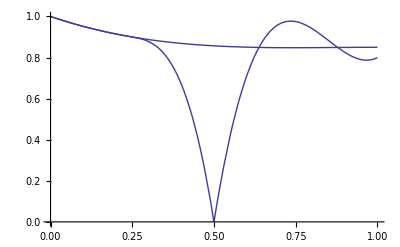

```mathematica
range={{0,1},{0,1}}

ptsFerroPara={{{0},1},{{1/4},0.9},{{1},0.85,0}};
lineFerroPara=Interpolation[ptsFerroPara];
(* make sure the 2 lines are tangent when they split *)
deriv=D[lineFerroPara[x],x]/.x->1/4;
ptsFerroMod={{{1/4},0.9,deriv},{{1/2},0,-10}};
lineFerroMod=If[x<1/4,lineFerroPara,Interpolation[ptsFerroMod]];
ptsModAnti={{{1/2},0,+10},{{1},0.8,0.8}};
lineModAnti=If[x<1/2,2,Interpolation[ptsModAnti]];
pFerroPara=Plot[lineFerroPara[x],{x,0,1},PlotRange->range];
pFerroMod=Plot[lineFerroMod[x],{x,0,1},PlotRange->range];
pModAnti=Plot[lineModAnti[x],{x,0,1},PlotRange->range];
Show[pFerroMod,pFerroPara,pModAnti]
```

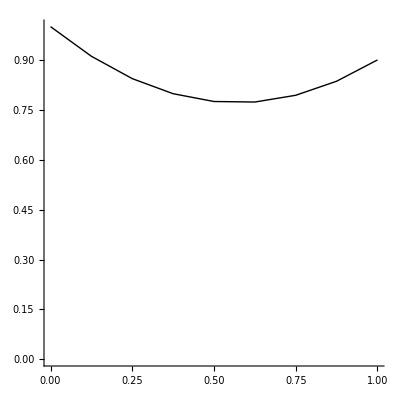

```mathematica
lineFerroPara=BezierCurve[{{0,1},{0.5,0.6},{1,0.9}}];
lineFerroMod=BezierCurve[{{
Graphics[{lineFerroPara},PlotRange->range,Axes->True]
```

## Chapter 2

### Renormalization real space

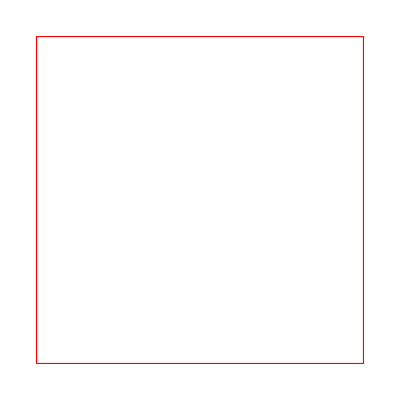

```mathematica
Graphics[{FaceForm[{Black,Opacity[0]}],EdgeForm[{Thick,Red}],Rectangle[{0,0},{1,1},RoundingRadius->.1]}]
```

```mathematica
rect[coordslow_,coordsup_,color_,thickness_]:={FaceForm[{Black,Opacity[0]}],EdgeForm[{thickness,color}],Rectangle[coordslow,coordsup,RoundingRadius->.1]}
```

```mathematica
Manipulate[Graphics[rect[{0,0},{1,1},RGBColor[r,g,b],Thickness[u]]],{u,0.01,0.2},{r,0,1},{g,0,1},{b,0,1}]
```

```mathematica
(* list of grid points coordinates *)
gridptscoords[origin_,numb_,size_]:=Flatten[Table[{i,j},{i,origin[[1]],origin[[1]]+size,size/numb},{j,origin[[2]],origin[[2]]+size,size/numb}],1]
```

```mathematica
gridpts[numb_,origin_,size_,radius_]:={PointSize[radius],Point/@gridptscoords[origin,numb,size]}
```

```mathematica
Manipulate[Graphics[gridpts[n,{0,0},2,r]],{n,1,10},{r,0.01,0.2}]
```

```mathematica
bluish=RGBColor[0.414,0.496,0.74];
```

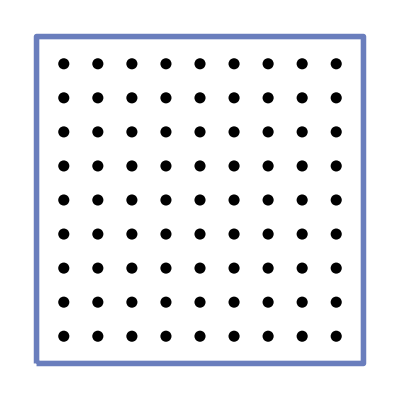

```mathematica
(* points + frame *)
δ=0.1;
Graphics[{rect[{0-δ,0-δ},{1+δ,1+δ},bluish,Thickness[0.01]],gridpts[8,{0,0},1,0.02]}]
```

```mathematica
(* coords is an array {coordslow, coordsup} *)
spinblock[coordslow_,delta_,thickness_]:={rect[coordslow-delta,coordslow+{1,1}+delta,bluish,Thickness[thickness]]}
```

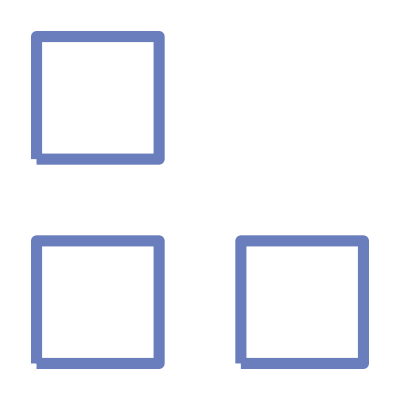

```mathematica
Graphics[{spinblock[{0,0},0.1,.02],spinblock[{2,0},0.1,.02],spinblock[{0,2},0.1,.02]}]
```

```mathematica
spinblockcoords=Flatten[Table[{x,y},{x,0,8,1.5},{y,0,8,1.5}],1];
```

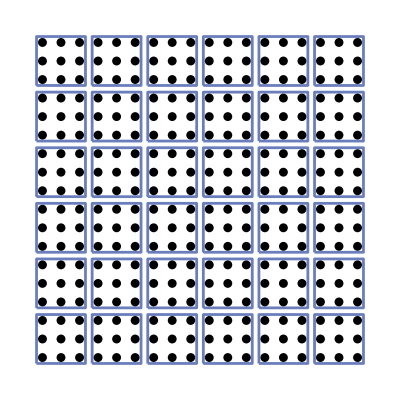

```mathematica
radius=0.016;
Graphics[{spinblock[#,0.16,0.005]&/@spinblockcoords,gridpts[8,{0,0},4,radius],gridpts[8,{4.5,0},4,radius],gridpts[8,{0,4.5},4,radius],gridpts[8,{4.5,4.5},4,radius]}]
```

```mathematica
(* after integration over spin blocks *)
newgridptscoords=Flatten[Table[{x,y},{x,0.5,8.5,1.5},{y,0.5,8.5,1.5}],1];
```

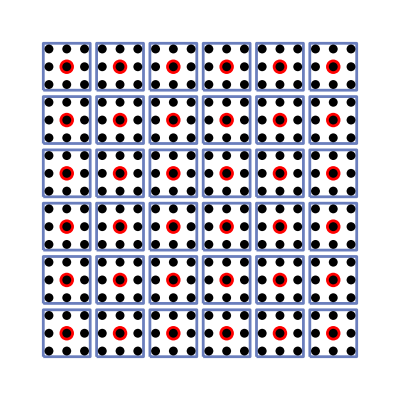

```mathematica
delta=0.35;
Graphics[{{PointSize[radius+.01],Red,Point/@newgridptscoords},{spinblock[#,0.16,0.005]&/@spinblockcoords,gridpts[8,{0,0},4,radius],gridpts[8,{4.5,0},4,radius],gridpts[8,{0,4.5},4,radius],gridpts[8,{4.5,4.5},4,radius]}},PlotRange->{{0-delta,8.5+delta},{0-delta,8.5+delta}}]
```

#### Export

```mathematica
nbdir=NotebookDirectory[]
```

/home/nicolas/git/reports/M2/report/img/generating/

```mathematica
exptdir=StringDrop[nbdir,-StringLength["generating/"]]<>"chap2/"
```

/home/nicolas/git/reports/M2/report/img/chap2/

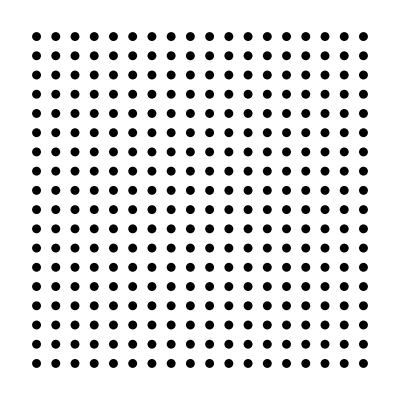

/home/nicolas/git/reports/M2/report/img/chap2/renorm_step0.pdf

```mathematica
radius=0.016;
Graphics[{gridpts[8,{0,0},4,radius],gridpts[8,{4.5,0},4,radius],gridpts[8,{0,4.5},4,radius],gridpts[8,{4.5,4.5},4,radius]}]
Export[exptdir<>"renorm_step0.pdf",%]
```

```mathematica
radius=0.016;
Graphics[{spinblock[#,0.16,0.005]&/@spinblockcoords,gridpts[8,{0,0},4,radius],gridpts[8,{4.5,0},4,radius],gridpts[8,{0,4.5},4,radius],gridpts[8,{4.5,4.5},4,radius]}]
Export[exptdir<>"renorm_step1.svg",%]
```

-Graphics-

/home/nicolas/git/reports/M2/report/img/chap2/renorm_step1.svg

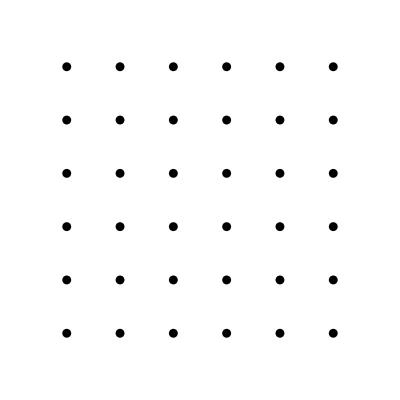

/home/nicolas/git/reports/M2/report/img/chap2/renorm_step2.pdf

```mathematica
delta=0.35;
newgridptscoords=Flatten[Table[{x,y},{x,0.5,8.5,1.5},{y,0.5,8.5,1.5}],1];
Graphics[{PointSize[radius],Point/@newgridptscoords},PlotRange->{{0-delta,8.5+delta},{0-delta,8.5+delta}}]
Export[exptdir<>"renorm_step2.pdf",%]
```

### Regulator

```mathematica
nbdir=NotebookDirectory[];
exptdir=StringDrop[nbdir,-StringLength["generating/"]]<>"chap2/"
```

/home/nicolas/git/reports/M2/report/img/chap2/

```mathematica
R[q_,k_,a_]:=-Tanh[q/k-a/k]+1
```

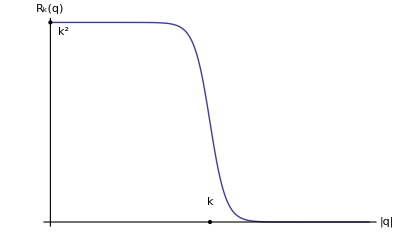

/home/nicolas/git/reports/M2/report/img/chap2/regulator.pdf

```mathematica
ptk={PointSize[Medium],Point[{1,0}],Text["k",{1,0.2}]};
ptk2={PointSize[Medium],Point[{0,2}],Text["k^2",{0.08,1.9}]};
Plot[R[q,0.1,1],{q,0,2},AxesLabel->{"|q|","R_k(q)"},Ticks->None,Epilog->{ptk,ptk2}]
Export[exptdir<>"regulator.pdf",%]
```